## Exercise 2, part (3)

```mathematica
λ0=1;
λ1=4/3;
yCritical=3.20;
fY[λ_,y_]:=1/λ ⅇ^(-y/λ)
```

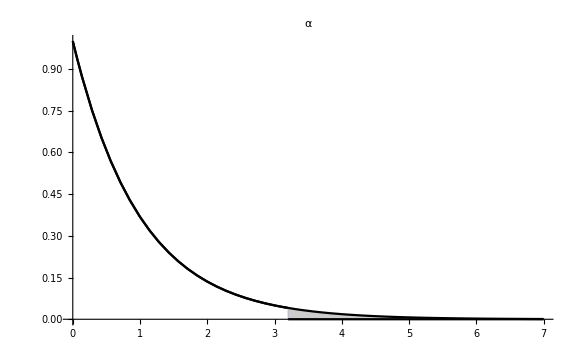

```mathematica
Plot[{If[y≥yCritical,0,fY[λ0,y]],fY[λ0,y]},{y,0,7},PlotRange->All,PlotStyle->{Black},Filling->{2},ImageSize->Large,PlotLabel->"α"]
```

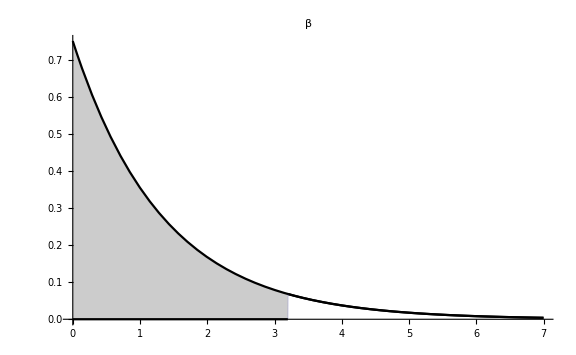

```mathematica
Plot[{If[y<yCritical,0,fY[λ1,y]],fY[λ1,y]},{y,0,7},PlotRange->All,PlotStyle->{Black},Filling->{2},ImageSize->Large,PlotLabel->"β"]
```

```mathematica
1-Sum[(ⅇ^-4 4^k)/(k!),{k,0,2}]//N
```

0.761897

## Exercise 4

```mathematica
ages={{1543,40},{1600,34},{1665,23},{1746,40},{1774,31},{1839,33},{1858,49},{1864,33},{1896,34},{1901,43},{1905,26},{1926,39}};
```

```mathematica
Mean[Transpose[ages][[2]]]//N
```

35.4167

```mathematica
Variance[Transpose[ages][[2]]]//N
```

52.2652

```mathematica
Sqrt[%]
```

7.22946

```mathematica
InverseCDF[StudentTDistribution[11],0.975]
```

2.20099

```mathematica
35.4-2.20 7.23/Sqrt[12]//N
```

30.8083

```mathematica
35.4+2.20 7.23/Sqrt[12]//N
```

39.9917

Part 2

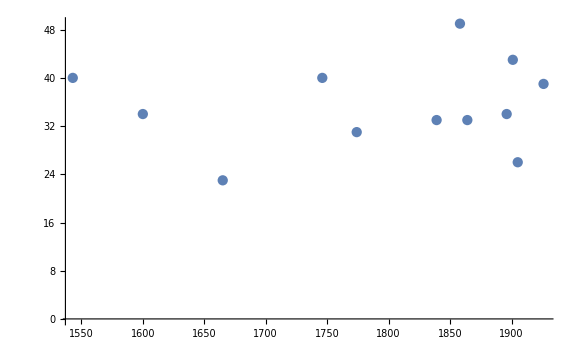

```mathematica
ListPlot[ages,ImageSize->Large]
```

This shows no particular distribution seems to be independent of time. Therefore we have no reason to doubt that μ remains constant over time.